# Coursework Part 2

## Exercise 1

{{0,-(ⅈ Ω)/2},{(ⅈ Ω)/2,0}}

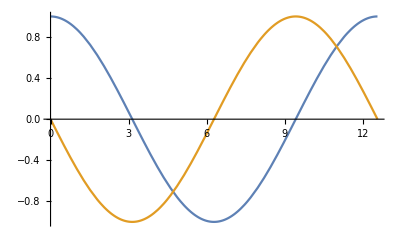

```mathematica
wMatrixRWA=Ω/2 PauliMatrix[2];
stateVec=Table[Subscript[c, i][t],{i,2}];
initStateVec={1,0};
tdseEqnsRWA=Table[{Subscript[c, i]'[t]==I(wMatrixRWA.stateVec)[[i]],Subscript[c, i][0]==initStateVec[[i]]},{i,2}];
tMax=4 Pi;
solRWA=NDSolve[tdseEqnsRWA/.Ω->1,stateVec,{t,0,tMax}];
solFnRWA=stateVec/.First[solRWA];
Plot[solFnRWA,{t,0,tMax}]
```

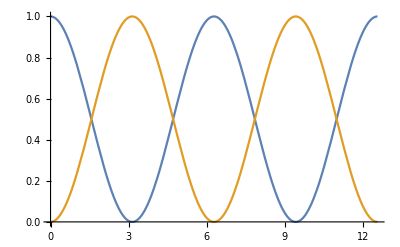

```mathematica
solFnRWAProb=Abs[solFnRWA]^2;
Plot[solFnRWAProb,{t,0,tMax}]
```

i) The plot shows the probabilities for the upper (blue line) and lower (red line) eigenstate as functions of time after setting up the system as in the upper energy state and letting it evolve with time.

ii) same problem with σ_x

{{0,Ω/2},{Ω/2,0}}

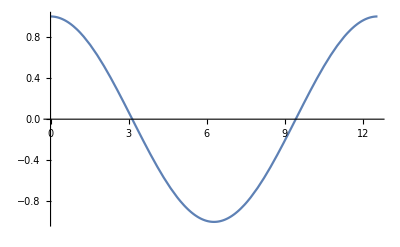

-Graphics-

```mathematica
wMatrixRWA=Ω/2 PauliMatrix[1];
tdseEqnsRWA=Table[{Subscript[c, i]'[t]==I(wMatrixRWA.stateVec)[[i]],Subscript[c, i][0]==initStateVec[[i]]},{i,2}];
solRWA=NDSolve[tdseEqnsRWA/.Ω->1,stateVec,{t,0,tMax}];
solFnRWA=stateVec/.First[solRWA];
Plot[solFnRWA,{t,0,tMax}]
solFnRWAProb=Abs[solFnRWA]^2;
Plot[solFnRWAProb,{t,0,tMax}]
```

## Exercise 2

iii)

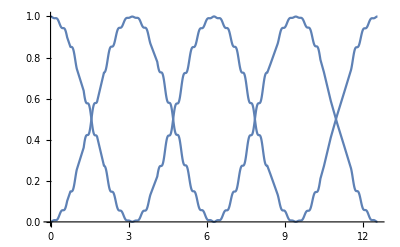

```mathematica
wMatrixLab=-w12/2 PauliMatrix[3]-Ω Cos[ω t] PauliMatrix[2]/.w12->ω+Δ;
tdseEqns=Table[{Subscript[c, i]'[t]==I(wMatrixLab.stateVec)[[i]],Subscript[c, i][0]==initStateVec[[i]]},{i,2}];
tdseSolraw= NDSolve[tdseEqns/.{ω->10Ω, Δ-> 0}/.Ω-> 1, stateVec, {t,0,tMax}];
tdseSol=stateVec/.First[tdseSolraw];
Plot[Abs[tdseSol]^2,{t,0,tMax}]
```

## Exercise 3

iv)

```mathematica
wMatrixRWA = -Ω/2 PauliMatrix[1]-{{0,0},{0,-Δ}};
T=MatrixExp[-I wMatrixRWA t] ;
RWAstatevec = T.initStateVec;
RWAstatevec//MatrixForm
```

(-(ⅇ^(1/2 ⅈ t (-Δ-√(Δ^2+Ω^2))) (Δ-√(Δ^2+Ω^2)))/(2 √(Δ^2+Ω^2))+(ⅇ^(1/2 ⅈ t (-Δ+√(Δ^2+Ω^2))) (Δ+√(Δ^2+Ω^2)))/(2 √(Δ^2+Ω^2))
-(ⅇ^(1/2 ⅈ t (-Δ-√(Δ^2+Ω^2))) Ω)/(2 √(Δ^2+Ω^2))+(ⅇ^(1/2 ⅈ t (-Δ+√(Δ^2+Ω^2))) Ω)/(2 √(Δ^2+Ω^2)))

v)

```mathematica
RWAstatevec/.Ω->1
Simplify[RWAstatevec/.{Ω->0}]
```

{-(ⅇ^(1/2 ⅈ t (-Δ-√(Δ^2))) (Δ-√(Δ^2)))/(2 √(Δ^2))+(ⅇ^(1/2 ⅈ t (-Δ+√(Δ^2))) (Δ+√(Δ^2)))/(2 √(Δ^2)),1}

{(ⅇ^(-1/2 ⅈ t (Δ+√(Δ^2))) ((-1+ⅇ^(ⅈ t √(Δ^2))) Δ+(1+ⅇ^(ⅈ t √(Δ^2))) √(Δ^2)))/(2 √(Δ^2)),0}